```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
If[!DirectoryQ["plots"],CreateDirectory["plots"]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.;
ωmax=4.;
Amin=0.0;
Amax=0.1;
M=16;
M2=3;
κ=1;
η=0.1;
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;

A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(ω^2*2*I*n+ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1+(-1)^j*Δ)*Cos[q/2]*(KroneckerDelta[i,j+1]+KroneckerDelta[i,j-1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]

A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1-(-1)^i*Δ)*Cos[q/2]*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];

findroot[a0_,ω_,Δ_,q_]:=Module[{g,a},g[a_?NumericQ]:=Max[Re[Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]]];
{a,g[a]}/.FindRoot[g[a],{a,a0}]]
```

/Users/zack/Documents/oscillators/snakingoscillators

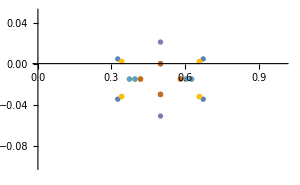
-Graphics- | {{π/2,{0.909769,0.909769,0.909769,0.909769}},{(3 π)/2,{0.909769,0.909769,0.909769,0.909769}},{(3 π)/4,{0.909769,0.827668,1.00001,0.909769}},{(5 π)/4,{0.909769,0.827668,1.00001,0.909769}},{π/4,{0.817129,1.01291,0.817129,1.01291}},{(7 π)/4,{0.817129,1.01291,0.817129,1.01291}},{0,{0.804272,1.0291,0.804272,1.0291}},{π,{0.725212,0.828717,1.14129,0.998748}}}

```mathematica
f[a_,ω_,Δ_,q_]:=Cases[Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],u_/;Im[u]≤1&&Im[u]>0]
a=0.0975238;
ω=3.32215;
Grid[{{ListPlot[Table[{Im[#],Re[#]}&/@f[a,ω,0.35,q],{q,0,2*Pi-4*Pi/M,4*Pi/M}],PlotRange->{{0,1},{-0.1,0.05}},ImageSize->300],
SortBy[Table[{q,Abs[Exp[2*Pi*f[a,ω,0.35,q]]]},{q,0,2*Pi-4*Pi/M,4*Pi/M}],Max[#[[2]]]&]}}]
```

{31.5183,Null}

{1.6436,Null}

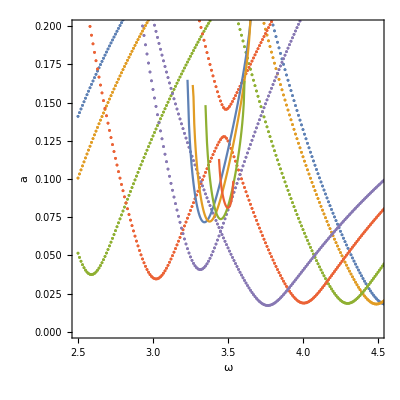

```mathematica
Δ=0.25;

tongues={};
ω0=3.4;
a0=0.08;
ωmin=2.5;
ωmax=5.0;

AbsoluteTiming[Monitor[Do[tongue={};
a=a0;
ω=ω0;
continue=True;While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω+dω;If[ω>ωmax||Abs[err]>10^-6,continue=False]; {ω-dω,a,err}];];
a=a0;
ω=ω0;
continue=True;
While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω-dω;If[ω<ωmin||Abs[err]>10^-6,continue=False]; {ω+dω,a,err}];];
AppendTo[tongues,tongue];{ω0,a0}=(First@MinimalBy[tongue,#[[2]]&])[[{1,2}]];,{q,0,Pi-4*Pi/M,4*Pi/M}],{ω,q}]]

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,Pi,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[i]]]],{i,1,Length[pds]}],PlotRange->{0,0.2}];
Show[p0,ListPlot[SortBy[#,#[[1]]&]&/@tongues[[All,All,{1,2}]],Joined->True],PlotRange->{{2.5,4.5},{0,0.2}},Axes->False,Frame->True,FrameLabel->{"ω","a"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

$Aborted

{2.76291,Null}

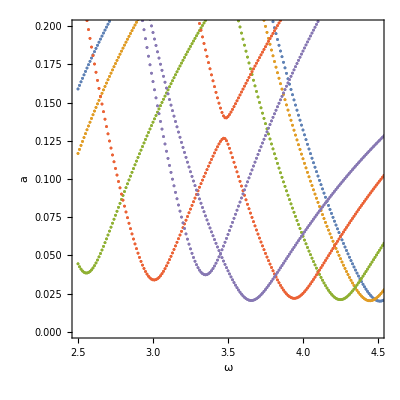

```mathematica
Δ=0.25;

tongues={};
ω0=3.3;
a0=0.1;
ωmin=2.5;
ωmax=5.0;
M=16;

AbsoluteTiming[Monitor[Do[tongue={};
a=a0;
ω=ω0;
continue=True;While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω+dω;If[ω>ωmax||Abs[err]>10^-6,continue=False]; {ω-dω,a,err}];];
a=a0;
ω=ω0;
continue=True;
While[continue,AppendTo[tongue,{a,err}=Quiet[findroot[a,ω,Δ,q]];ω=ω-dω;If[ω<ωmin||Abs[err]>10^-6,continue=False]; {ω+dω,a,err}];];
AppendTo[tongues,tongue];{ω0,a0}=(First@MinimalBy[tongue,#[[2]]&])[[{1,2}]];,{q,0,Pi-4*Pi/M,4*Pi/M}],{ω,q}]]

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,Pi,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[i]]]],{i,1,Length[pds]}],PlotRange->{0,0.2}];
Show[p0,ListPlot[SortBy[#,#[[1]]&]&/@tongues[[All,All,{1,2}]],Joined->True],PlotRange->{{2.5,4.5},{0,0.2}},Axes->False,Frame->True,FrameLabel->{"ω","a"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]
```

```mathematica
(*Find the smallest Δ supporting solitons (and the frequency)*)
```

{2.8571,Null}

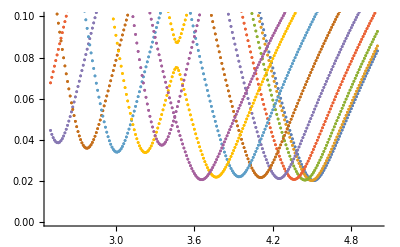

```mathematica
tongues={};
ω0=3.3;
a0=0.1;
ωmin=2.5;
ωmax=5.0;
M=32;
Δ=0.25;

AbsoluteTiming[pds=Table[ParallelTable[{evals,evecs}=Eigensystem[{A4[ω,Δ,q,0.5],B4[ω]}];cases=Abs[Re[Cases[evals,u_/;Abs[Im[u]]<10^-6]]];Transpose[{ConstantArray[ω,Length[cases]],ConstantArray[q,Length[cases]],cases}],{ω,ωmin,ωmax,0.01}] ,{q,0,Pi,4*Pi/M}];]
p0=Show[Table[ListPlot[pds[[i,All,All,{1,3}]],PlotStyle->Directive[PointSize[0.005],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,1,Length[pds]}],PlotRange->{0,0.1}]
```

```mathematica
Cases[Flatten[pds,2],u_/;u[[1]]==3.5]
```

{{3.5,0,0.347553},{3.5,0,0.347553},{3.5,0,0.306832},{3.5,0,0.306832},{3.5,π/8,0.340019},{3.5,π/8,0.340019},{3.5,π/8,0.301511},{3.5,π/8,0.301511},{3.5,π/4,0.318066},{3.5,π/4,0.318066},{3.5,π/4,0.285665},{3.5,π/4,0.285665},{3.5,(3 π)/8,0.283582},{3.5,(3 π)/8,0.283582},{3.5,(3 π)/8,0.259581},{3.5,(3 π)/8,0.259581},{3.5,π/2,0.239733},{3.5,π/2,0.239733},{3.5,π/2,0.223424},{3.5,π/2,0.223424},{3.5,(5 π)/8,0.191133},{3.5,(5 π)/8,0.191133},{3.5,(5 π)/8,0.176907},{3.5,(5 π)/8,0.176907},{3.5,(3 π)/4,0.140833},{3.5,(3 π)/4,0.140833},{3.5,(3 π)/4,0.122789},{3.5,(3 π)/4,0.122789},{3.5,(7 π)/8,0.0916298},{3.5,(7 π)/8,0.0916298},{3.5,(7 π)/8,0.0694447},{3.5,(7 π)/8,0.0694447},{3.5,π,0.0637276},{3.5,π,0.0637276},{3.5,π,0.0399428},{3.5,π,0.0399428}}

```mathematica
Simplify[(Exp[x]-Exp[-x])/(Exp[x]+Exp[-x])/.x->Log[r]]
```

(-1+r^2)/(1+r^2)

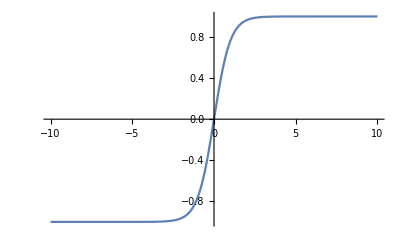

```mathematica
Plot[(Exp[x]-Exp[-x])/(Exp[x]+Exp[-x]),{x,-10,10}]
```

```mathematica
filebase="data/pendula73";
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
nT=1000;
Grid[{{Grid[{{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M+1]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,ColorFunction->cf]]}}]},{rasterizeBackground[ListPlot[Transpose[{Cos[dat[[1;;nT,1;;M]]]+Transpose[ConstantArray[Range[nT],M]],Sin[dat[[1;;nT,1;;M]]]+2*ConstantArray[Range[M],nT]},{3,2,1}],Joined->True,ImageSize->1000,AspectRatio->1/4,Axes->False]]}}]
```

{32,2000.,1000.,0.05,0.05,3.45}

-Graphics- | -Graphics-
-Graphics-

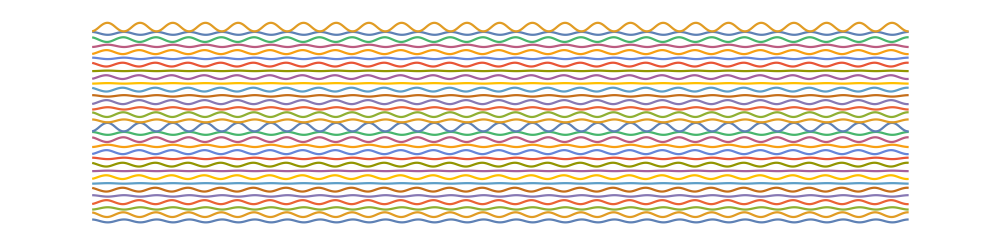

```mathematica
ListPlot[Transpose[{Transpose[ConstantArray[Range[nT],M]],dat[[1;;nT,1;;M]]+2*ConstantArray[Range[M],nT]},{3,2,1}],Joined->True,ImageSize->1000,AspectRatio->1/4,Axes->False]
```